# Creating a Name Plate

Christopher Hanusa
http://qc.edu/~chanusa
chanusa@qc.cuny.edu

## Shapes

### Shape Examples

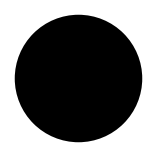

```mathematica
Graphics[Disk[{0,0},5]]
```

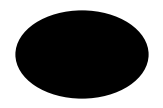

```mathematica
Graphics[Disk[{0,0},{6,4}]]
```

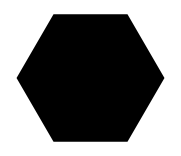

```mathematica
Graphics[RegularPolygon[6]]
```

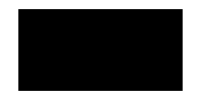

```mathematica
Graphics[Rectangle[{0,0},{2,1}]]
```

### Code to Discretize:

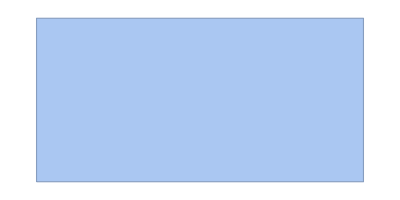

```mathematica
shape=DiscretizeGraphics[Graphics[Rectangle[{0,0},{2,1}]]]
```

## Images

### Drag and drop your image here.

```mathematica
flower=-Graphics-;
```

### Code to discretize.

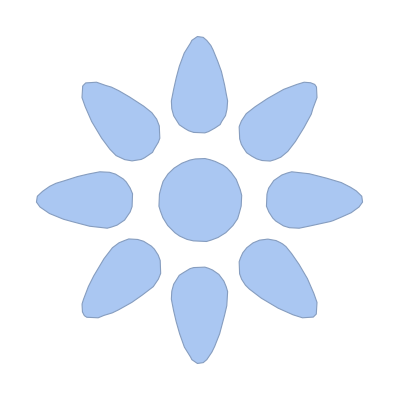

```mathematica
image=ImageMesh[ColorNegate[flower]]
```

## Text

```mathematica
word=Text[Style["word",Bold,FontFamily->"Bauhaus 93",FontSize->50]]
```

word

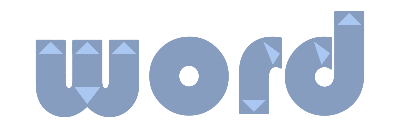

```mathematica
text=DiscretizeGraphics[word,_Text]
```

## Resize and overlap

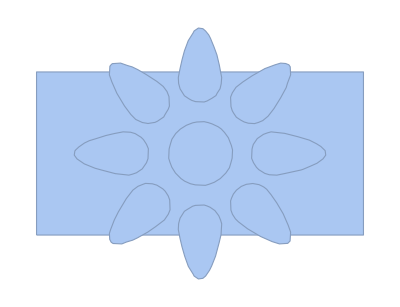

```mathematica
resizedShape=RegionResize[shape,1.3];
resizedImage=RegionResize[image,1];
translatedShape=TransformedRegion[resizedShape,TranslationTransform[-Map[Mean,RegionBounds[resizedShape]]]];
translatedImage=TransformedRegion[resizedImage,TranslationTransform[-Map[Mean,RegionBounds[resizedImage]]]];
Show[translatedShape,translatedImage]
```

```mathematica
background=translatedShape;
foreground=translatedImage;
middle=BoundaryDiscretizeRegion[RegionDifference[background,foreground]]
```

```mathematica
outerboundary=RegionBoundary[background];
innerboundary=RegionBoundary[foreground];
```

```mathematica
nameplate=Show[{
RegionProduct[background,Point[{{0.}}]],
RegionProduct[outerboundary,Line[{{0.},{.1}}]],
RegionProduct[middle,Point[{{.1}}]],
RegionProduct[innerboundary,Line[{{.1},{.2}}]],
RegionProduct[foreground,Point[{{.2}}]]
}]
```

```mathematica
Export[NotebookDirectory[]<>"nameplate.stl",nameplate]
```